```mathematica
Quit[]
```

# Compare q^2 distributions for all decays

## Init

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

### Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957061;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

### Clear

```mathematica
Clear[Fq3π1,Fq2π,Fq3π,Fq4π,Fq5π,Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ3π1,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

### Analytical results for Math

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4, Fq3π,Fq5π,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
```

### File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

### evtGen interface

```mathematica
evtPDL=ReadString["../evt.pdl"];
```

```mathematica
(* selecting only ccq decays *)
decCC=Select[decays,!StringFreeQ[#⟦1⟧,"{cc}"]&];
partsCC=DeleteDuplicates@Flatten@decCC;
```

```mathematica
Clear[evtName];
evtName::usage="evtName[name] --- transforms name of the particle to EvtGen format";
evtName[p_]:=StringReplace[p,{"\\"->"","{"->"","}"->"","^"->""}];
evtName["\\Xi_{c}^{\\prime0}"]="Xi'_c0";
evtName["\\Xi_{c}^{\\prime+}"]="Xi'_c+";
Clear[evtMass]
evtMass::usage="evtMass[name] --- reads mass of the particle from evtPDL (loaded evt.pdl file)";
evtMass[p_]:=Module[{x},
x=StringCases[evtPDL,Shortest[evtName[p]~~__~~id:NumberString~~" "~~__~~m:NumberString]:>{id,m}];
If[Length[x]≥1,Return[ToExpression[x⟦1,-1⟧]]];
Print["Particle ",p," is absent in evt.pdl"];
Return[10];
];
```

### Functions to compare MATH and ROOT

```mathematica
decTemplate="
noPhotos
Decay IN
1 OUT    e+  anti-nu_e  PHOTOS OMEGAOMEGA;
Enddecay
End
";
Clear[genDecMC];
genDecMC::usage="genDecMC[{in, out}] --- runs baryons.exe to simulate in -> out e nu decay and reads q^2 distribution";
genDecMC[{p1_,p2_}]:=Module[{},
PrintTemporary["Decay ",p1,"->",p2];
PrintTemporary["\t constructing decay file"];
{ep1,ep2}=evtName/@{p1,p2};
dec=StringReplace[decTemplate,{"IN"->ep1,"OUT"->ep2}];
WriteString["dec.dec",dec];
PrintTemporary["\t running baryons.exe"];
Run["../baryons.exe "<>ep1<>" dec.dec 100000"];
PrintTemporary["\t extracting m2_23 distr"];
Run["../rrF.exe -v m2_23 -s"];
tab=ReadList["m2_23.txt",{Number,Number,Number}]⟦All,1;;2⟧;
PrintTemporary["\t Clearing the results"];
DeleteFile/@{"evtOutput.root","out.root","m2_23.txt","dec.dec"};
Return[tab];
];
```

```mathematica
Clear[genDecMath];
genDecMath::usage="genDecMath[{in, out}] --- returns q^2 distribution of in -> out e nu decays in the spectral functions framework";
genDecMath[{in_,out_}]:=Module[{},
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
{m1,m2}=evtMass/@{in,out};
{m3,m4}={0,0};
Return[Table[{m232,dΓl},{m232,0,(m1-m2)^2,(m1-m2)^2/50}]];
];
```

```mathematica
Clear[normHST];
normHST::usage="normHST[table] returns normalized to 1 table";
normHST[xxx_]:=Module[{int},
int=NIntegrate[Interpolation[xxx][q2],{q2,xxx⟦1,1⟧,xxx⟦-1,1⟧}];
Return[{#⟦1⟧,#⟦2⟧/int}&/@xxx]
];
```

## RUN

```mathematica
(* generating MC and Math tables for all cc decays *)
Clear[tabMC, tabMath];
AbsoluteTiming[
Do[
Print["======= ",i,"/",Length[decCC]];
$dec=decCC⟦i⟧;
tabMC[i] = normHST[genDecMC[$dec]];
tabMath[i]= normHST[genDecMath[$dec]];
,{i,Length[decCC]}];
]
```

======= 1/10

======= 2/10

======= 3/10

======= 4/10

======= 5/10

======= 6/10

======= 7/10

======= 8/10

======= 9/10

======= 10/10

{86.2747,Null}

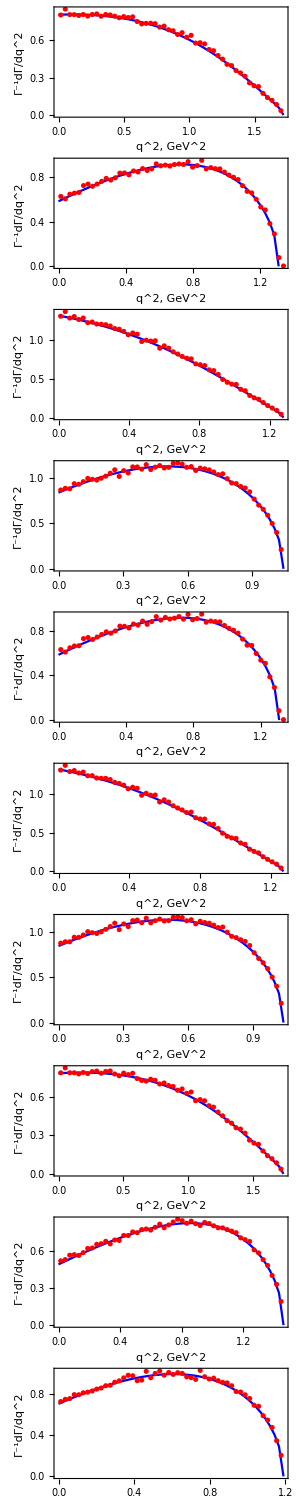

```mathematica
(* show the plots *)
GraphicsGrid[#,ImageSize->300]&@Table[{
ListPlot[{tabMC[i],tabMath[i]}, Joined->{False,True}, PlotStyle->{Red,Blue}, FrameLabel->{"q^2, GeV^2","Γ^-1dΓ/dq^2"}, Frame->True]
},{i,Length[decCC]}]
```